# Assignment 09

## On Probability Distribution and Monte Carlo Method

PH 1050 Computational Physics

Aarya Gosar (EP23B025)

Engineering Physics

25th Oct 2023

## Introduction

Monty Carlo is a way to numerically solve the problem using random numbers and exploiting the central limit theorem to get a precise approximation of the solution. In this assignment we first study how to create random numbers and their various distributions. In the second part we use the Monte Carlo method to integrate and check validity of CLT.

## Aim

#### Part 1

1) Creating pseudorandom numbers and seeing their distribution.
2) computing statistical values of two different distribution.
3) Verifying CLT for a non-normal distribution.

#### Part 2

1) Computing the value of Pi 
2) Integrating single variable function 
3) integrating multivariable function

## Code

### Part1 Probability Distribution

#### Creating PseudoRandom numbers

We can see that for a bifurcation model, we get pseudorandom numbers for large R

{}

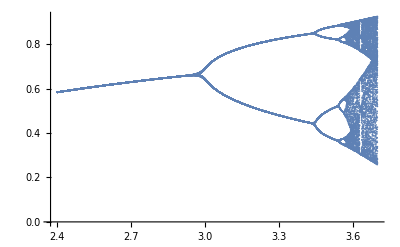

```mathematica
P={x0};
x0=0.1;
n=100;
maxBi=30;
model[x_]=R (x-x^2);

Data={}
For[R=2.4,R<3.7,R=R+0.0005,P={x0};
For[i=2,i<=n,i++,AppendTo[P,model[P[[i-1]]]]];
For[i=0,i<maxBi,i++,AppendTo[Data,{R,P[[n-i]]}]];]
ListPlot[Data]
```

Using this chaotic behaviour at a large R

```mathematica
R = 3.899;
model[x_]=R (x-x^2);
x0=0.2;
P={x0};
n = 100000;
For[i=2,i<=n,i++,AppendTo[P,model[P[[i-1]]]]];
```

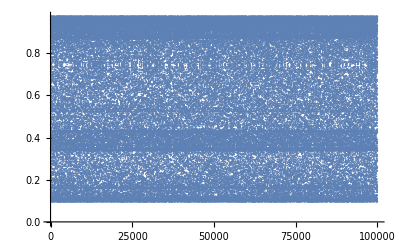

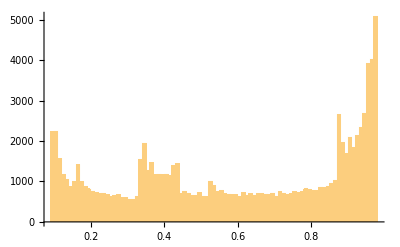

```mathematica
ListPlot[P]
Histogram[P,100]
```

This is not a Uniform distribution, this model has tendencies to go towards certain values, but they are still pseudorandom
(as we can see there are bands forming in the listplot, it would be interesting to see why those bands exist)

#### Statistical measures for two different distribution

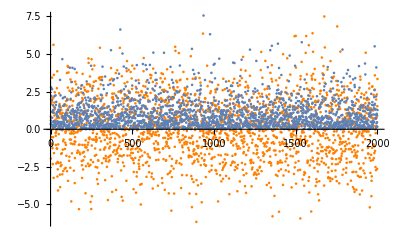

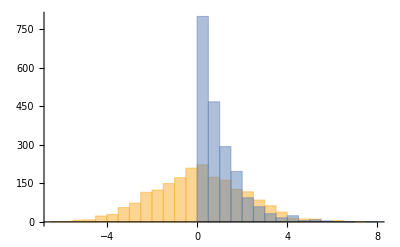

```mathematica
datExp = RandomVariate[NormalDistribution[0,2],n];
datExp2 = RandomVariate[ExponentialDistribution[1],n];
Show[{ListPlot[datExp, PlotStyle->Orange],ListPlot[datExp2]}]
Histogram[{datExp,datExp2}]
```

Means

```mathematica
Mean[datExp]
Mean[datExp2]
```

0.0802406

0.983997

Variance

```mathematica
Variance[datExp]
Variance[datExp2]
```

4.03955

0.947836

```mathematica
Covariance[datExp,datExp2]
```

-0.0015145

Skewness

```mathematica
Skewness[datExp]
Skewness[datExp2]
```

0.0542331

1.94367

kurtosis

```mathematica
Kurtosis[datExp]
Kurtosis[datExp2]
```

3.01648

8.12456

#### Verifying Central Limit theorem

We will use uniform distribution.

i =

1

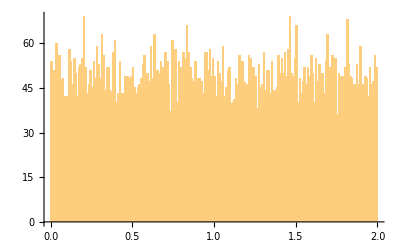

i =

2

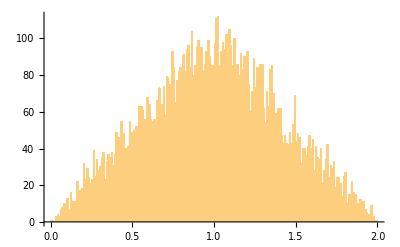

i =

3

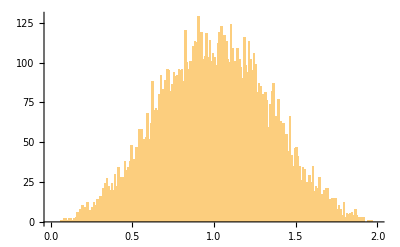

```mathematica
For[ i = 1 , i <= 3, i++, 
avgs = {};
For[j=1,j <= 10000, j++,
AppendTo[avgs,Mean[RandomReal[{0,2} , i]]]
];
Print["i = "];
Print[i];
Print[Histogram[avgs,{0,2,0.01}]]
]
```

### Part 2 Using Monte Carlo Method

#### For Computing π

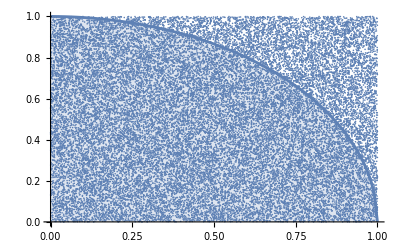

3.14437

```mathematica
Clear["Global`*"]
pltCircle = ListLinePlot[Table[{x,Sqrt[1-x^2]} , {x,0,1,0.01}], Filling->Bottom];
pts = {};
a = 0;
b = 0;
For[i = 1 , i<30000, i++ ,

x = RandomReal[{0,1}];
y = RandomReal[{0,1}];
b = b + 1;
If[x^2 + y^2 <= 1, a = a + 1;];
AppendTo[pts,{x,y}];
]
pltPoints = ListPlot[pts];
Show[{pltPoints , pltCircle}]
4 a / b // N
```

This value is close enough to 3.141

#### For Integrating single variable function

The function I have used is

```mathematica
Clear["Global`*"]
a = 1;
b = 3;
n = 2000;
f[x_] =Exp[-3 x ] Cos[x]/(1+Sinh[2*x]*(Log[x])^2)
```

(ⅇ^(-3 x) Cos[x])/(1+Log[x]^2 Sinh[2 x])

The actual value of integration is

```mathematica
NIntegrate[f[x] , {x,a,b}]
```

0.00415512

Using Monte Carlo

```mathematica
sum = 0;
For[j = 1, j <= n, j++,
sum = sum + (b-a) * f[RandomReal[{a,b}]]/ n
];
sum
```

0.0042621

Verifying CLT For this by repeating it 1000 times

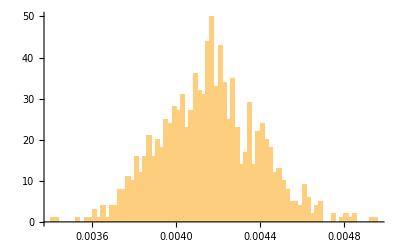

```mathematica
avgs = {};
For[i=1, i <= 1000, i ++ ,
sum = 0;
For[j = 1, j <= n, j++,
sum = sum + (b-a) * f[RandomReal[{a,b}]]/ n
];
AppendTo[avgs, sum]
]
Histogram[avgs, 100]
```

The peak should give predicted value

```mathematica
h = HistogramList[avgs, 100];
h[[1]][[Flatten[Position[h[[2]],Max[h[[2]]]]][[1]]]] // N
```

0.00416

This is a more accurate value

### Doing the same for Multivariable

The Function is

```mathematica
Clear["Global`*"]
f[x_, y_] = Log[1 + x^2 + y^2] Exp[π/(1 + x)] Sin[y]
a = 2;
b = π;
n = 2000;
```

ⅇ^(π/(1+x)) Log[1+x^2+y^2] Sin[y]

```mathematica
avgs = {};
For[i=1, i <= 1000, i ++ ,
sum = 0;
For[j = 1, j <= n, j++,
sum = sum + (b-a)^2 * f[RandomReal[{a,b}] , RandomReal[{a,b}]]/ n
];
AppendTo[avgs, sum]]
```

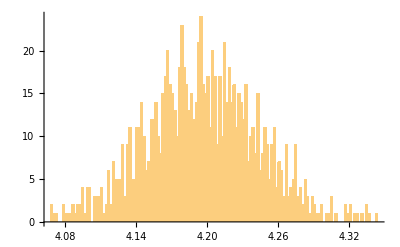

```mathematica
Histogram[avgs, 100]
```

```mathematica
h = HistogramList[avgs, 100 ];
h[[1]][[Flatten[Position[h[[2]],Max[h[[2]]]]][[1]]]] // N
```

4.194

The actual value of integration is

```mathematica
NIntegrate[f[x,y] , {x,a,b},{y,a,b}]
```

4.195

## Conclusion/Comments

1) CLT is valid for these MonteCarlo integrations
2) The Equation we used is similar to that of Rienmann Sum. But taking Random values helps us to exploit CLT
3) In Rienmann sum, we take steps at regular interval. This is why we need to take random values in Uniform Distribution for MonteCarlo